```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/8.1/8.1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/8.1/~$8.1.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/8.1/8.1.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

## Dataset 1

```mathematica
dataset1 = makeDataset[raw⟦2⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs = dataset1[All, <|"lnT"-> (Around[#lnT,#dlnT] &), "lnW" -> (#lnW &)|>]
```

Dataset[<>]

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
```

```mathematica
datasetline =raw⟦2⟧⟦2;;⟧⟦All,1;;2⟧
```

{{7.17012,-0.0639414},{7.24794,0.290698},{7.32221,0.575056},{7.37971,0.760689},{7.41482,1.01244},{7.50533,1.26574},{7.57237,1.557},{7.62152,1.76161},{7.6708,2.01335},{7.7173,2.17345},{7.7393,2.26088}}

```mathematica
line1 = LinearModelFit[datasetline,{1,x},x]
```

FittedModel[-29.0977+4.05143 x]

```mathematica
line1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -29.0977 | 0.432021 | -67.3524 | 1.7708×10^-13
x | 4.05143 | 0.0576821 | 70.2372 | 1.21486×10^-13

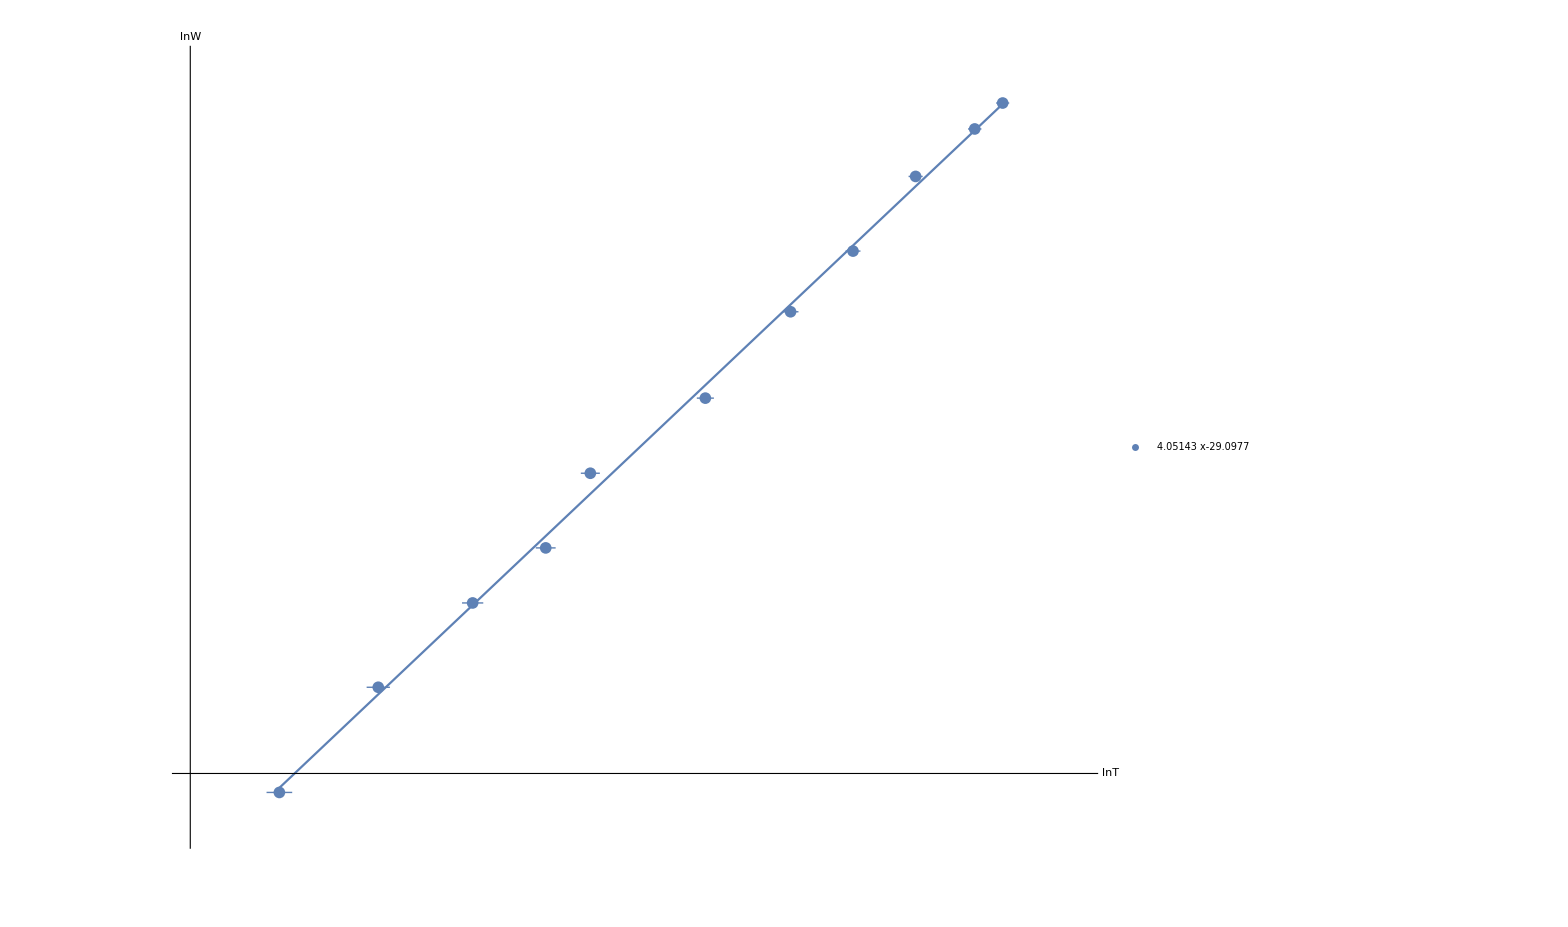

```mathematica
Show[
ListPlot[
{dataset1WithErrs},
PlotRange-> {{7.1,7.8},{-0.2,2.4}},
Ticks-> {Range[-1000,1000, 0.05],Range[-1000,1000, 0.2]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["lnT", Large], Style["lnW", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 0.01],Range[-1000,1000, 0.05]},
LabelStyle->Black,
PlotLegends->Placed[LineLegend[
{Normal@line1},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.3],Scaled[0.75]}
]
],
Plot[line1[x],{x,7.170,7.739}]
]
```

```mathematica
( (π^2*(1.38049*10^-23)^4)/(60*(3*10^8)^2*4.95*10^-8) )^(1/3)*2π
```

6.9288×10^-34

```mathematica
( (π^2*(1.38049*10^-23)^4)/(60*(3*10^8)^2*5.6696*10^-8) )^(1/3)*2π
```

6.6223×10^-34

```mathematica
2π((π^2*(1.38049*10^-23)^4)/(60*(3*10^8)^2))^(1/3)*1/3*(4.95*10^-8)^(-4/3)0.13*10^-8
```

6.06561×10^-36

```mathematica
A = {{7,-6},{-6,7}}
```

{{7,-6},{-6,7}}

```mathematica
{{1/7,0},{0,1/7}}.{{0,-6},{-6,0}}//MatrixForm
```

(0 | -6/7
-6/7 | 0)

```mathematica
Eigensystem@
```

```mathematica
2/(1.0+√(13/49))
```

1.32006

```mathematica
L = {{10, 0, 0 ,0},{2, 10, 0,0},{-3,2,10,0},{-3,2,
```

```mathematica
8.0/9
```

0.888889

```mathematica
2.0/(1+√(1-36/49))
```

1.32006

```mathematica
6.0/19
```

0.315789

```mathematica
2.0/13
```

0.153846

```mathematica
2.0/(1+√(1-9/25))
```

1.11111

```mathematica
1/7.0
```

0.142857

```mathematica
Solve[{V * √2/2.0 + (V0-u)*(-1/2) ==u &&V*√2/2 - (V0 - u) * √3/2 ==0},{V0, u}]
```

{{V0→1.11536 V,u→0.298858 V}}